## Задание 1.

Спроектируйте и создайте функции для построения выпуклой оболочки заданного множества точек плоскости с использованием алгоритма Джарвиса . Проведите тестирование .

```mathematica
ClearAll[NamedQ,𝔨𝔪];
(** Атрибуты и описание **)
𝔨𝔪::usage="Knowledge base «computer mathematics»";
SetAttributes[𝔨𝔪,{Protected,ReadProtected}];
NamedQ::usage="Check: is there a name of tested equations";
NamedQ[n1_,n2__]:=And[NamedQ[n1],NamedQ[n2]];
SetAttributes[NamedQ,Listable];
```

```mathematica
ClearAll[kmPoint];
(** Атрибуты и описание **)
SetAttributes[kmPoint,ReadProtected];
kmPoint::usage="Point on the surface";
(** Свойства **)
NamedQ[kmPoint[𝔨𝔪,id_String,___]]^:=id≠"";
kmPoint[𝔨𝔪,_String,coord_List,___]["coord"]:=coord;
kmPoint[𝔨𝔪,id_String,___]["id"]:=If[id=="","Point",id];
(** Конструкторы **)
kmPoint[id_String,coord:{_,_}]:=kmPoint[𝔨𝔪,id,coord];
kmPoint[coord:{_,_}]:=kmPoint[𝔨𝔪,"",coord];
kmPoint[{L1_kmLine,L2_kmLine}]:=kmPoint[#[[2]]&/@(First@NSolve@Through[{L1,L2}@"equ"])]
(** Декораторы **)
Format[P_kmPoint,StandardForm]:=Row@{P["id"],"(",Row[P["coord"],","],")"};
```

```mathematica
ClearAll[kmVector];
(** Атрибуты и описание **)
SetAttributes[kmVector,ReadProtected];
kmVector::usage="Vector on the surface";
(** Свойства **)
NamedQ[kmVector[𝔨𝔪,id_String,___]]^:=id≠"";
kmVector[𝔨𝔪,id_String,___]["id"]:=If[id=="","Vector",id];
kmVector[𝔨𝔪,_String,coord_List,___]["coord"]:=coord;
kmVector[𝔨𝔪,_String,coord_List,___]["norm"]:=Sqrt[Plus@@(coord*coord)];
(** Конструкторы **)
kmVector[id_String,coord_List]:=kmVector[𝔨𝔪,id,coord];
kmVector[coord_List]:=kmVector[𝔨𝔪,"",coord];
kmVector[id_String,P0_kmPoint,P1_kmPoint]:=kmVector[id,P1@"coord"-P0@"coord"];
kmVector[P0_kmPoint,P1_kmPoint]:=kmVector[
If[NamedQ[P0,P1],StringJoin[P0@"id",P1@"id"],""],P0,P1];
(** Декораторы **)
MakeBoxes[V_kmVector,StandardForm]^:=TemplateBox[{V@"id",
RowBox@Riffle[MakeBoxes[#,StandardForm]&/@V["coord"],","]
},"Point2D",
DisplayFunction:>(RowBox@{OverscriptBox[#1,"⇀"],"(",#2,")"}&),
InterpretationFunction->(RowBox@{"{",#2,"}"}&),
Tooltip->Automatic];
```

```mathematica
Q=kmPoint[{RandomReal[{-10,10}],RandomReal[{-10,10}]}]&/@Range[20]
```

{Point(,,-6.10506-4.1234),Point(,,7.27459-8.9774),Point(,,-3.524630.490719),Point(,,-1.53621-1.68081),Point(,,7.372254.91439),Point(,,-4.491113.32172),Point(,,-0.745309-2.31505),Point(,,-2.34098-3.54808),Point(,,-6.43925-9.06982),Point(,,-0.675399-4.34603),Point(,,-5.301969.90214),Point(,,5.459152.63591),Point(,,4.837147.90777),Point(,,-7.48234-7.53143),Point(,,6.274998.84135),Point(,,9.595712.16887),Point(,,-9.963932.85043),Point(,,2.445516.91267),Point(,,6.363617.56487),Point(,,5.933795.27948)}

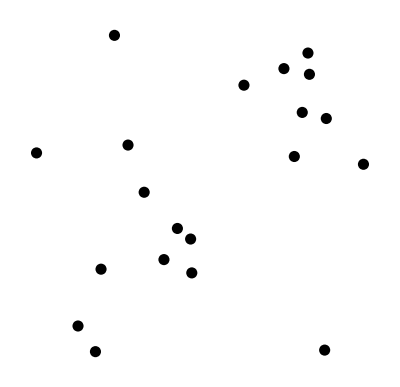

```mathematica
pointsPicture=Graphics[{PointSize@0.02,Point[#["coord"]]&/@Q}]
```

```mathematica
StartPoint=Q[[1]]
```

Point(,,-6.10506-4.1234)

```mathematica
For[
i=2,i<=Length@Q,i++,
If[
And[
Or[
Q[[i]]["coord"][[2]]<StartPoint["coord"][[2]],
Q[[i]]["coord"][[2]]==StartPoint["coord"][[2]]
],
Q[[i]]["coord"][[1]]<StartPoint["coord"][[1]]
],
StartPoint=Q[[i]]
]
]
```

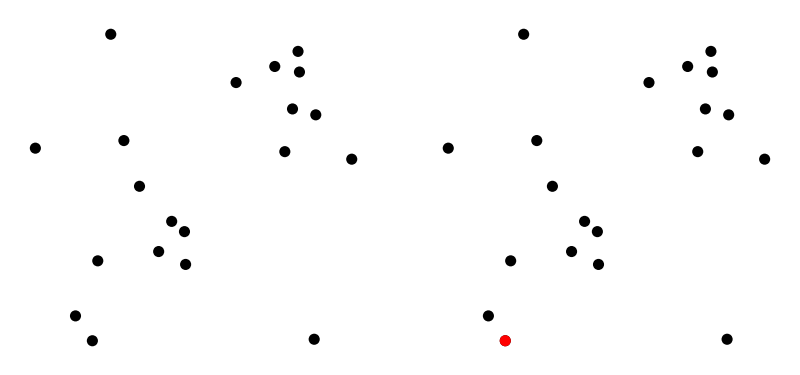

```mathematica
pointsPictureWithStartPoint=Graphics[{PointSize@0.02,Point[#["coord"]]&/@Q,Red,Point@StartPoint["coord"]}];
GraphicsRow[{pointsPicture,pointsPictureWithStartPoint},Frame->All]
```

```mathematica
L={StartPoint};
NextPoint=First@Q
CurrentPoint=Last[L]
```

Point(,,-6.10506-4.1234)

Point(,,-6.43925-9.06982)

```mathematica
getTriangleAlgebraicSquare[points_List]:=Module[{a=points[[1]]["coord"],b=points[[2]]["coord"],c=points[[3]]["coord"]},1/2 Det[{b-a,c-a}]]
```

```mathematica
algebraicSquares=getTriangleAlgebraicSquare[{CurrentPoint,NextPoint,#}]&/@Q
```

Det::luc: Result for Det of badly conditioned matrix {{0.314562,12.542},{0.314562,12.542}} may contain significant numerical errors.

{-7.44667×10^-17,-11.8114,0.,7.92549,-39.4084,-71.7101,10.3606,-84.1259,-102.594,-70.4049,-26.9876,-37.2905,-7.77494,-47.8924,-52.8802,16.1753,-56.8334,2.3798,-81.875,0.0565533}

```mathematica
Q1=First@Q[[#]]&/@(Position[algebraicSquares[[#]]>0&/@Range[Length@algebraicSquares],True])
Q2=First@Q[[#]]&/@(Position[algebraicSquares[[#]]<0&/@Range[Length@algebraicSquares],True])
```

{Point(,,-8.15156-4.63301),Point(,,-8.265366.31257),Point(,,-9.42543-2.97049),Point(,,-7.29594-5.77817),Point(,,-6.54819.26802)}

{Point(,,-6.65444.67005),Point(,,-4.83961.93105),Point(,,-0.53451-1.88267),Point(,,4.723162.37096),Point(,,6.48142-6.46487),Point(,,9.766587.09522),Point(,,4.691589.41055),Point(,,-2.6228-6.17331),Point(,,-0.946726-4.85252),Point(,,-5.71739-7.40362),Point(,,0.867920.0923001),Point(,,1.708351.88858),Point(,,2.325841.3736),Point(,,6.21657-2.71379)}

```mathematica
pointsPictureWithStartOfAlgorithm=Graphics[{PointSize@0.02,Blue,PointSize@0.02,Point[#["coord"]]&/@Q1,
Red,Point[#["coord"]]&/@Q2,
Black,Line[{CurrentPoint["coord"],NextPoint["coord"]}]}];
```

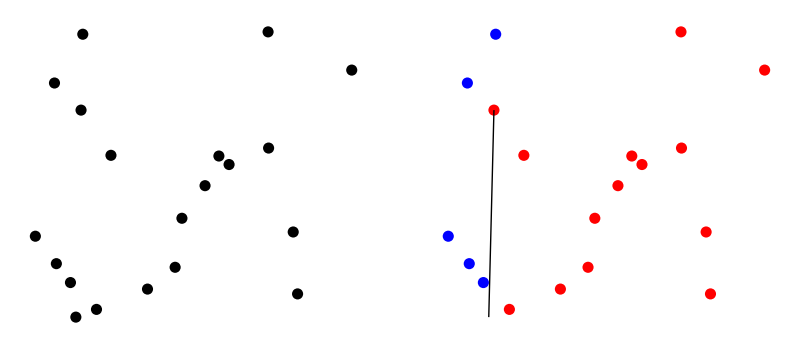

```mathematica
GraphicsRow[{pointsPicture,pointsPictureWithStartOfAlgorithm},Frame->All]
```

```mathematica
isPointOnLine[Line_kmLine,P_kmPoint]:=Line["equ"]/.{x->P["coord"][[1]],y->P["coord"][[2]]}
```

```mathematica
Unprotect[Unequal]
```

{Unequal}

```mathematica
Unequal[Point1_kmPoint,Point2_kmPoint]:=Point1["coord"]!=Point2["coord"]
```

```mathematica
Q[[3]]!=Q[[5]]
```

True

Важно закинуть стартовую точку в конец Q.

```mathematica
getStartPoint[Q_List]:=Module[{StartPoint=Q[[1]]},
For[
i=2,i<=Length@Q,i++,
If[
And[
Or[
Q[[i]]["coord"][[2]]<StartPoint["coord"][[2]],
Q[[i]]["coord"][[2]]==StartPoint["coord"][[2]]
],
Q[[i]]["coord"][[1]]<StartPoint["coord"][[1]]
],
StartPoint=Q[[i]]
]
];
Return@StartPoint
]
```

```mathematica
moveToEndOfList[lst_List,obj_]:=Append[DeleteCases[lst,obj],obj]
```

```mathematica
CH[points_List]:=Module[{i=1,StartPoint,CurrentPoint,NextPoint,algebraicSquare,L},
StartPoint=getStartPoint[Q];
L=AppendTo[L,StartPoint];
Q=moveObjToEnd[Q,StartPoint];
CurrentPoint=StartPoint;
NextPoint=Q[[1]];
While[
CurrentPoint!=NextPoint,
Do[
algebraicSquare=getTriangleAlgebraicSquare[{CurrentPoint,NextPoint,i}];
If[algebraicSquare>0,NextPoint=i],
{i,Q}
];
Q=DeleteCases[Q,NextPoint];
L=AppendTo[L,NextPoint];
CurrentPoint=NextPoint;
NextPoint=Q[[1]]
];
Return@L
]
```

```mathematica
CH[Q]
```

before{Point(,,-6.65444.67005),Point(,,-4.83961.93105),Point(,,-6.96896-7.87192),Point(,,-8.15156-4.63301),Point(,,-0.53451-1.88267),Point(,,4.723162.37096),Point(,,-8.265366.31257),Point(,,6.48142-6.46487),Point(,,9.766587.09522),Point(,,4.691589.41055),Point(,,-2.6228-6.17331),Point(,,-0.946726-4.85252),Point(,,-5.71739-7.40362),Point(,,0.867920.0923001),Point(,,1.708351.88858),Point(,,-9.42543-2.97049),Point(,,2.325841.3736),Point(,,-7.29594-5.77817),Point(,,6.21657-2.71379),Point(,,-6.54819.26802)}

After{Point(,,-6.65444.67005),Point(,,-4.83961.93105),Point(,,-8.15156-4.63301),Point(,,-0.53451-1.88267),Point(,,4.723162.37096),Point(,,-8.265366.31257),Point(,,6.48142-6.46487),Point(,,9.766587.09522),Point(,,4.691589.41055),Point(,,-2.6228-6.17331),Point(,,-0.946726-4.85252),Point(,,-5.71739-7.40362),Point(,,0.867920.0923001),Point(,,1.708351.88858),Point(,,-9.42543-2.97049),Point(,,2.325841.3736),Point(,,-7.29594-5.77817),Point(,,6.21657-2.71379),Point(,,-6.54819.26802),Point(,,-6.96896-7.87192)}

Point(,,-6.65444.67005)

Point(,,-4.83961.93105)

Point(,,-8.15156-4.63301)

Point(,,-0.53451-1.88267)

Point(,,4.723162.37096)

Point(,,-8.265366.31257)

Point(,,6.48142-6.46487)

Point(,,9.766587.09522)

Point(,,4.691589.41055)

Point(,,-2.6228-6.17331)

Point(,,-0.946726-4.85252)

Point(,,-5.71739-7.40362)

Point(,,0.867920.0923001)

Point(,,1.708351.88858)

Point(,,-9.42543-2.97049)

Point(,,2.325841.3736)

Point(,,-7.29594-5.77817)

Point(,,6.21657-2.71379)

Point(,,-6.54819.26802)

```mathematica
algebraicSquares=getTriangleAlgebraicSquare[{CurrentPoint,NextPoint,#}]&/@DeleteCases[Q,NextPoint]
```

{-33.9018,-5.61093,-10.8916,-31.8221,-2.74758,-12.9536,-9.21324,0.,-13.4659,0.357417,-27.4713,-25.052,2.83685,-28.4521,-37.7799,10.7091,-19.3033,-28.8846,-28.2034}

```mathematica
Q
```

{Point(,,-6.10506-4.1234),Point(,,7.27459-8.9774),Point(,,-3.524630.490719),Point(,,-1.53621-1.68081),Point(,,7.372254.91439),Point(,,-4.491113.32172),Point(,,-0.745309-2.31505),Point(,,-2.34098-3.54808),Point(,,-6.43925-9.06982),Point(,,-0.675399-4.34603),Point(,,-5.301969.90214),Point(,,5.459152.63591),Point(,,4.837147.90777),Point(,,-7.48234-7.53143),Point(,,6.274998.84135),Point(,,9.595712.16887),Point(,,-9.963932.85043),Point(,,2.445516.91267),Point(,,6.363617.56487),Point(,,5.933795.27948)}